```mathematica
kC = 3 * 10^10;
kR = 83144626.1815324;            
kHplank = 6.62 * 10^-27;
kb = 1.3807 * 10^-16;
kSt = 6.65210 * 10^-25; 
 kMhydrogen = 1.6735575 * 10^-24;
kStefanBoltzmann = 5.670374419 * 10^-5; 
eV=241799050402417.;
A=(2 kb^4)/(kC^2 kHplank^3);
f[x_]:=NIntegrate[t^3/(Exp[t]-1),{t,0,x}]
f0[x_]:= Piecewise[{{x^3(1/3-x/8+x^2/62.4),x≤2},{Pi^4/15-Exp[-x](x^3+3 x^2+6x+7.28),x>2}}]
```

0.00762079

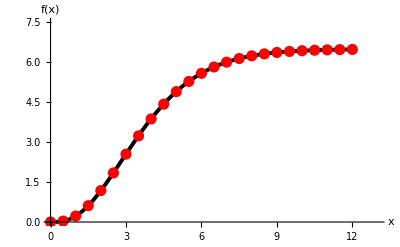

```mathematica
Max[Table[Abs[f[x]-f0[x]],{x,3,5,0.01}]]
F=Table[{x,f0[x]},{x,0,12,0.5}];
Show[Plot[f[x],{x,0,12}, PlotRange->{{0,13},{0,Pi^4/15+1}},PlotStyle->Directive[Black,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],
AxesLabel->{"x","f(x)"}], ListPlot[F, PlotStyle->Directive[Red, PointSize[0.02]]]]
```

```mathematica
T=27.282;
v1=10^17;
v0=0;
A*(f0[ (kHplank v1)/(kb T)]-f0[(kHplank v0)/(kb T)])T^4
kStefanBoltzmann/Pi T^4
```

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

10.0144

9.99923

```mathematica
R=0.3;
U[r_,kin_,kout_, Q_]:=Q Piecewise[{{1/2 NIntegrate[(1-Exp[-kin(2 √(R^2-r^2(1-μ^2)))])Exp[-kout(r μ-√(R^2-r^2(1-μ^2)))],{μ,√(1-(R/r)^2),1}],r≥R},{NIntegrate[1-Cosh[kin r μ]Exp[-kin √(R^2-r^2(1-μ^2))],{μ,0,1}],r<R}}]
X=Table[i,{i,0,1,0.01}];
{kC/(100*10^-7),kC/(800*10^-7), (kC/(100*10^-7)-kC/(800*10^-7))/20.}//N;
V=Table[v,{v,3.33*10^14,3.*10^15,(kC/(100*10^-7)-kC/(800*10^-7))/50.}];

Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4
absorp[d_,T_,v1_,v0_]:=d/(4 A*Pi*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4)
```

```mathematica
sol=Table[{V[[i]],U[R,absorp[10^-4,1000,V[[i+1]],V[[i]]],absorp[10^-100,1000,V[[i+1]],V[[i]]], Ie[1000,V[[i+1]],V[[i]]]]}, {i,1,Length[V]-1}];
```

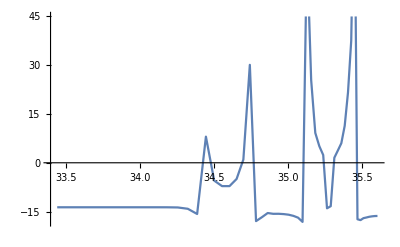

```mathematica
ListLinePlot[Log@sol]
```

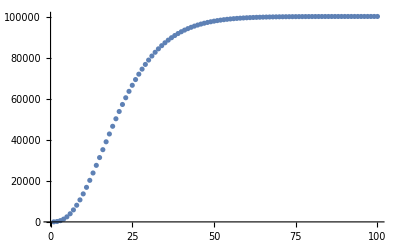

```mathematica
ListPlot[Table[Ie[273,x,0],{x,10^12,10^14,10^12}],PlotRange->All]
```

```mathematica
T=27.282;
v1=3*10^17;
v0=10^17;
Ie[T,v1,v0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-10.0144

```mathematica
q[x_]:=x^3+3 x^2+6x+7.28
IeLog[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)]q[V0]-Exp[-AA/2(V1-V0)]q[V1]]
```

```mathematica
IeLog[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
IeLog2[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)+Log[q[V0]]]-Exp[-AA/2(V1-V0)+Log[q[V1]]]]
IeLog2[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-175624.] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
IeLog3[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)-AA/4(V1-V0)+Log[Exp[3/2 AA/2(V1-V0)+Log[q[V0]]]-Exp[-1/2 AA/2(V1-V0)+Log[q[V1]]]]
IeLog3[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-87751.7] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
3/2(kHplank/(kb T))/2(v1-v0)+Log[q[v0]]
```

263735.

```mathematica
q0[x_]:=x^3(1/3-x/8+x^2/62.4)
IeLog5[AA_,V0_,V1_]:= 
Piecewise[{{Log[A*(q0[AA*V1]-q0[AA*V0])],AA*V1≤2},{Piecewise[{{ Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)]q[V0]-Exp[-AA/2(V1-V0)]q[V1]],AA/2(V1-V0)<700},{Log[A]-AA/2(V0+V1)+AA/2(V1-V0)+Log[q[V0]],AA/2(V1-V0)>=700}}],AA*V1>2}}]
```

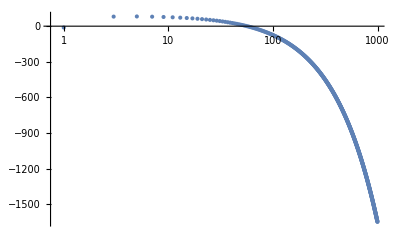

```mathematica
ListLogLinearPlot[Table[{x/10^14,Re@IeLog5[kHplank/(kb T*100),x-2*10^14,x]},{x,10^14,10^17,2*10^14}],PlotRange->All]
```

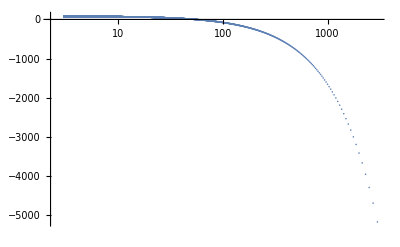

```mathematica
ListLogLinearPlot[Table[{(kC/λ)/10^14,IeLog5[kHplank/(kb T*100),kC/λ,kC/(λ-0.999*10^-7)]},{λ,1000*10^-7,0.1*10^-7,-0.1*10^-7}],PlotRange->All]
```

```mathematica
kStefanBoltzmann*T^4/Pi
Ie[T,10^14,0]
Exp[IeLog5[kHplank/(kb T),0,10^14]+4Log[T]]
```

9.99923

10.0144

11.2266

```mathematica
(*Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4*)
IeExp[AA_,V0_,V1_]:= A(Exp[-AA V0]q[V0]-Exp[-AA(V1)]q[V1])
IeExp[kHplank/(kb T),0,10^14]*T^4
Exp@IeLog5[kHplank/(kb T),0,10^20]*T^4
```

11.2266

11.2266

```mathematica
Table[x/10^14,{x,10^14,10^17,2*10^14}]//N ;
Table[λ,{λ,1000*10^-7,3*10^-7,-1*10^-7}]//N;
```

^2

```mathematica
Pi^4/15-q0[2]
```

5.31445

```mathematica
Pi^4/15-Exp[-2]*q[2]
```

1.17797

```mathematica
Log[5]//N
```

1.60944

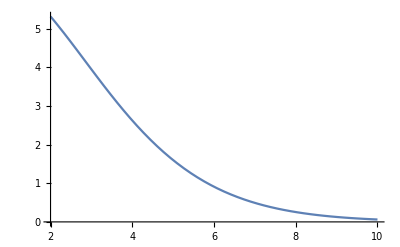

```mathematica
Plot[Exp[-x]*q[x],{x,2,10}]
```

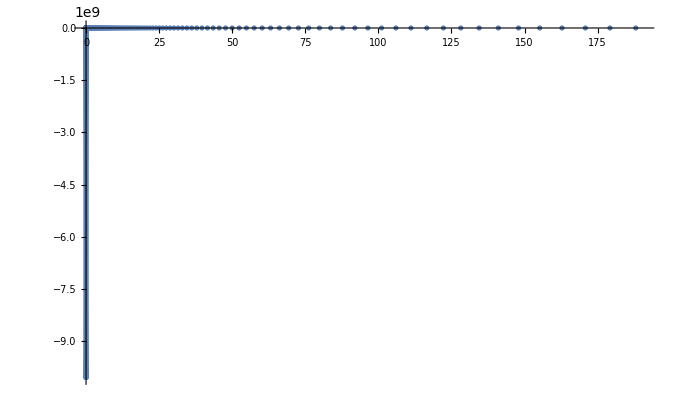

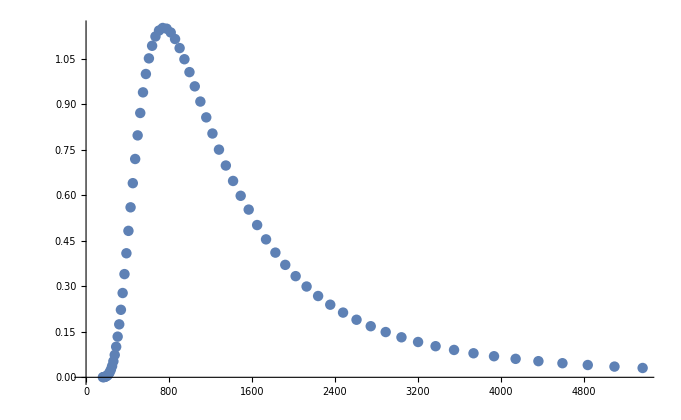

{{44890.2,9.96226},{47393.1,9.8022},{50038.4,9.64188},{52834.3,9.4813},{55789.7,9.32046},{58913.8,9.15938},{62216.4,8.99804},{65707.9,8.83647},{69399.2,8.67466},{73302.1,8.51261},{77429.,8.35033},{81792.9,8.18781},{86407.6,8.02508},{91287.9,7.86212},{96449.4,7.69894},{101909.,7.53554},{107683.,7.37192},{113791.,7.20809},{120252.,7.04405},{127087.,6.87981},{134319.,6.71535},{141970.,6.55069},{150066.,6.38582},{158632.,6.22075},{167697.,6.05548},{177291.,5.89002},{187443.,5.72435},{198188.,5.55849},{209562.,5.39243},{221600.,5.22618},{234344.,5.05973},{247835.,4.8931},{262117.,4.72627},{277238.,4.55925},{293248.,4.39205},{310200.,4.22466},{328152.,4.05707},{347161.,3.88931},{367294.,3.72135},{388615.,3.55322},{411198.,3.38489},{435119.,3.21639},{460457.,3.0477},{487298.,2.87883},{515733.,2.70978},{545859.,2.54054},{577778.,2.37113},{611598.,2.20153},{647435.,2.03175},{685411.,1.8618},{0,3.54066}}

General::munfl: Exp[-1.00304×10^10] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00295×10^10] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00281×10^10] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

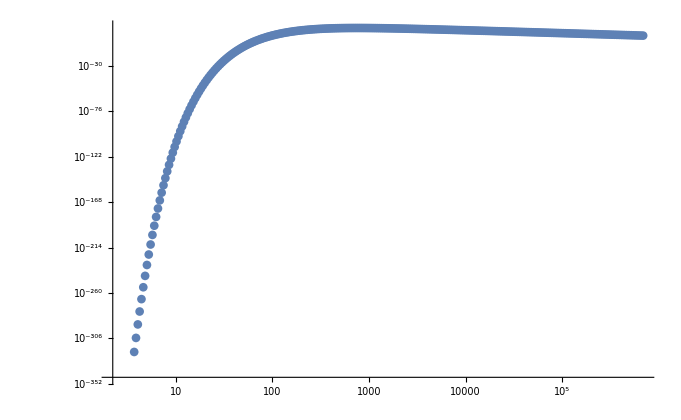

```mathematica
(*C++ расчёт*)
fplank=Import["/home/artem/projects/test/plank.txt","table"];
fplankL=Import["/home/artem/projects/test/plankL.txt","table"];
ListPlot[{fplank}]
ListPlot[Table[{fplank[[i,1]],(Exp@fplank[[i,2]])/(3 10^8)},{i,840,910}]]
Table[fplank[[i]],{i,950,Length@fplank}]
ListLogLogPlot[Table[{fplank[[i,1]],Exp@fplank[[i,2]]},{i,1,Length@fplank}]]
```

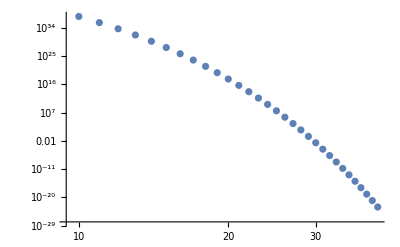

```mathematica
tem=10^4;
(*int[x,Inf]{sigmaT^4}*)
ListLogLogPlot[Table[{x/10^15,Exp[Re@IeLog5[kHplank/(kb tem),x,10^20]+4Log[tem]]},{x,10^16,4*10^16,10^15}],PlotRange->All]
```

```mathematica
(10^20-10^11)/1000//N
```

1.×10^17

-Graphics-

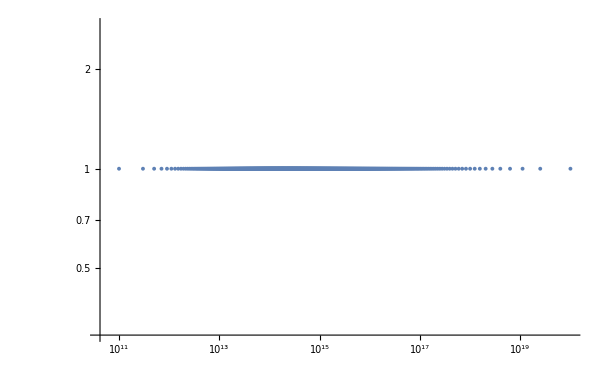

```mathematica
FF[x_]:=a 1/x^2+c
ans=NSolve[{FF[1]==10^20,FF[1000]==10^11},{a,c},Reals][[1]];
ListPlot[Table[{x,FF[x]/.ans},{x,1,1000}],PlotRange->All]
ListLogLogPlot[Table[{FF[x]/.ans,1},{x,1,1000}],PlotRange->All]
```

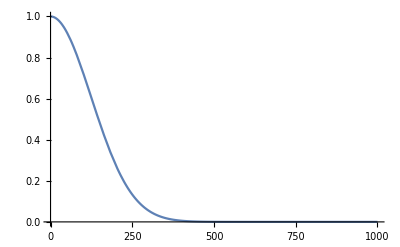

3.90469×10^-13

```mathematica
Plot[(a Exp[-x^2/b]+c)/.{a->1,b->31000,c->0},{x,0,1000},PlotRange->All]
(a Exp[-x^2/b]+c)/.{a->1,b->35000,c->0,x->1000}//N
```

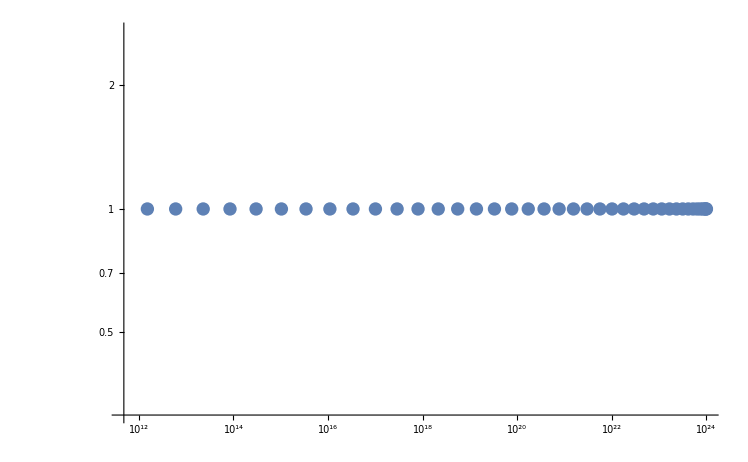

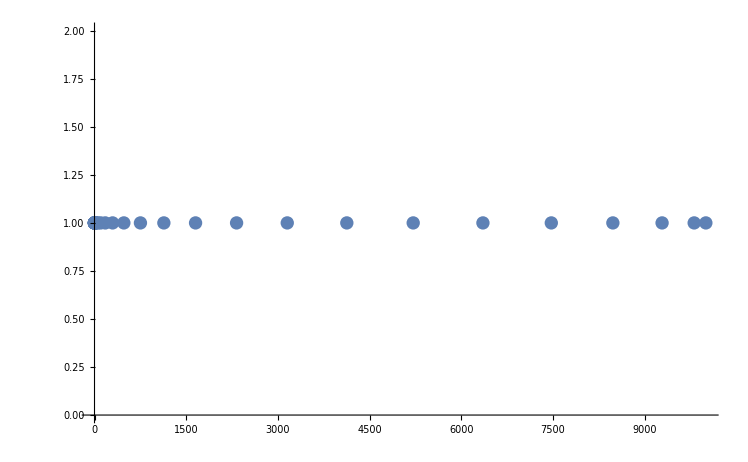

{{9.99971×10^23,1.},{9.99886×10^23,1.},{9.99743×10^23,1.},{9.99543×10^23,1.},{9.99286×10^23,1.},{9.98972×10^23,1.},{9.98601×10^23,1.},{9.98173×10^23,1.},{9.97688×10^23,1.},{9.97147×10^23,1.},{9.96549×10^23,1.},{9.95894×10^23,1.},{9.95183×10^23,1.},{9.94416×10^23,1.},{9.93592×10^23,1.},{9.92712×10^23,1.},{9.91777×10^23,1.},{9.90786×10^23,1.},{9.89739×10^23,1.},{9.88636×10^23,1.},{9.87479×10^23,1.},{9.86267×10^23,1.},{9.84999×10^23,1.},{9.83678×10^23,1.},{9.82301×10^23,1.},{9.80871×10^23,1.},{9.79387×10^23,1.},{9.77849×10^23,1.},{9.76258×10^23,1.},{9.74614×10^23,1.},{9.72916×10^23,1.},{9.71167×10^23,1.},{9.69365×10^23,1.},{9.67511×10^23,1.},{9.65605×10^23,1.},{9.63649×10^23,1.},{9.61641×10^23,1.},{9.59582×10^23,1.},{9.57474×10^23,1.},{9.55315×10^23,1.},{9.53107×10^23,1.},{9.50849×10^23,1.},{9.48543×10^23,1.},{9.46188×10^23,1.},{9.43785×10^23,1.},{9.41334×10^23,1.},{9.38836×10^23,1.},{9.36291×10^23,1.},{9.337×10^23,1.},{9.31063×10^23,1.},{9.2838×10^23,1.},{9.25652×10^23,1.},{9.22879×10^23,1.},{9.20062×10^23,1.},{9.17201×10^23,1.},{9.14297×10^23,1.},{9.1135×10^23,1.},{9.0836×10^23,1.},{9.05329×10^23,1.},{9.02256×10^23,1.},{8.99142×10^23,1.},{8.95988×10^23,1.},{8.92793×10^23,1.},{8.8956×10^23,1.},{8.86287×10^23,1.},{8.82976×10^23,1.},{8.79627×10^23,1.},{8.76241×10^23,1.},{8.72818×10^23,1.},{8.69358×10^23,1.},{8.65863×10^23,1.},{8.62333×10^23,1.},{8.58767×10^23,1.},{8.55168×10^23,1.},{8.51535×10^23,1.},{8.47869×10^23,1.},{8.44171×10^23,1.},{8.40441×10^23,1.},{8.36679×10^23,1.},{8.32887×10^23,1.},{8.29065×10^23,1.},{8.25213×10^23,1.},{8.21331×10^23,1.},{8.17422×10^23,1.},{8.13484×10^23,1.},{8.0952×10^23,1.},{8.05528×10^23,1.},{8.01511×10^23,1.},{7.97467×10^23,1.},{7.93399×10^23,1.},{7.89307×10^23,1.},{7.85191×10^23,1.},{7.81051×10^23,1.},{7.7689×10^23,1.},{7.72706×10^23,1.},{7.685×10^23,1.},{7.64274×10^23,1.},{7.60028×10^23,1.},{7.55762×10^23,1.},{7.51477×10^23,1.},{7.47174×10^23,1.},{7.42853×10^23,1.},{7.38515×10^23,1.},{7.3416×10^23,1.},{7.29789×10^23,1.},{7.25403×10^23,1.},{7.21001×10^23,1.},{7.16586×10^23,1.},{7.12157×10^23,1.},{7.07715×10^23,1.},{7.0326×10^23,1.},{6.98794×10^23,1.},{6.94316×10^23,1.},{6.89827×10^23,1.},{6.85328×10^23,1.},{6.8082×10^23,1.},{6.76303×10^23,1.},{6.71777×10^23,1.},{6.67244×10^23,1.},{6.62703×10^23,1.},{6.58155×10^23,1.},{6.53602×10^23,1.},{6.49042×10^23,1.},{6.44478×10^23,1.},{6.39909×10^23,1.},{6.35337×10^23,1.},{6.30761×10^23,1.},{6.26182×10^23,1.},{6.21601×10^23,1.},{6.17018×10^23,1.},{6.12434×10^23,1.},{6.07849×10^23,1.},{6.03264×10^23,1.},{5.9868×10^23,1.},{5.94096×10^23,1.},{5.89514×10^23,1.},{5.84933×10^23,1.},{5.80356×10^23,1.},{5.75781×10^23,1.},{5.71209×10^23,1.},{5.66641×10^23,1.},{5.62078×10^23,1.},{5.5752×10^23,1.},{5.52967×10^23,1.},{5.4842×10^23,1.},{5.43879×10^23,1.},{5.39345×10^23,1.},{5.34818×10^23,1.},{5.30299×10^23,1.},{5.25788×10^23,1.},{5.21286×10^23,1.},{5.16792×10^23,1.},{5.12308×10^23,1.},{5.07834×10^23,1.},{5.03371×10^23,1.},{4.98918×10^23,1.},{4.94476×10^23,1.},{4.90045×10^23,1.},{4.85627×10^23,1.},{4.81221×10^23,1.},{4.76828×10^23,1.},{4.72448×10^23,1.},{4.68081×10^23,1.},{4.63728×10^23,1.},{4.59389×10^23,1.},{4.55065×10^23,1.},{4.50756×10^23,1.},{4.46462×10^23,1.},{4.42184×10^23,1.},{4.37922×10^23,1.},{4.33676×10^23,1.},{4.29447×10^23,1.},{4.25235×10^23,1.},{4.2104×10^23,1.},{4.16862×10^23,1.},{4.12702×10^23,1.},{4.08561×10^23,1.},{4.04438×10^23,1.},{4.00334×10^23,1.},{3.96248×10^23,1.},{3.92182×10^23,1.},{3.88136×10^23,1.},{3.84109×10^23,1.},{3.80103×10^23,1.},{3.76116×10^23,1.},{3.7215×10^23,1.},{3.68205×10^23,1.},{3.64281×10^23,1.},{3.60379×10^23,1.},{3.56497×10^23,1.},{3.52638×10^23,1.},{3.488×10^23,1.},{3.44984×10^23,1.},{3.41191×10^23,1.},{3.37419×10^23,1.},{3.33671×10^23,1.},{3.29945×10^23,1.},{3.26243×10^23,1.},{3.22563×10^23,1.},{3.18907×10^23,1.},{3.15274×10^23,1.},{3.11664×10^23,1.},{3.08079×10^23,1.},{3.04517×10^23,1.},{3.00979×10^23,1.},{2.97465×10^23,1.},{2.93976×10^23,1.},{2.90511×10^23,1.},{2.8707×10^23,1.},{2.83654×10^23,1.},{2.80263×10^23,1.},{2.76896×10^23,1.},{2.73554×10^23,1.},{2.70237×10^23,1.},{2.66945×10^23,1.},{2.63677×10^23,1.},{2.60436×10^23,1.},{2.57219×10^23,1.},{2.54027×10^23,1.},{2.50861×10^23,1.},{2.4772×10^23,1.},{2.44604×10^23,1.},{2.41514×10^23,1.},{2.38449×10^23,1.},{2.3541×10^23,1.},{2.32396×10^23,1.},{2.29407×10^23,1.},{2.26444×10^23,1.},{2.23507×10^23,1.},{2.20595×10^23,1.},{2.17708×10^23,1.},{2.14847×10^23,1.},{2.12012×10^23,1.},{2.09202×10^23,1.},{2.06417×10^23,1.},{2.03658×10^23,1.},{2.00924×10^23,1.},{1.98216×10^23,1.},{1.95533×10^23,1.},{1.92875×10^23,1.},{1.90242×10^23,1.},{1.87635×10^23,1.},{1.85053×10^23,1.},{1.82496×10^23,1.},{1.79964×10^23,1.},{1.77457×10^23,1.},{1.74975×10^23,1.},{1.72517×10^23,1.},{1.70085×10^23,1.},{1.67677×10^23,1.},{1.65294×10^23,1.},{1.62936×10^23,1.},{1.60602×10^23,1.},{1.58292×10^23,1.},{1.56007×10^23,1.},{1.53745×10^23,1.},{1.51508×10^23,1.},{1.49295×10^23,1.},{1.47106×10^23,1.},{1.44941×10^23,1.},{1.42799×10^23,1.},{1.40681×10^23,1.},{1.38587×10^23,1.},{1.36516×10^23,1.},{1.34468×10^23,1.},{1.32443×10^23,1.},{1.30442×10^23,1.},{1.28463×10^23,1.},{1.26507×10^23,1.},{1.24574×10^23,1.},{1.22663×10^23,1.},{1.20775×10^23,1.},{1.18909×10^23,1.},{1.17065×10^23,1.},{1.15243×10^23,1.},{1.13443×10^23,1.},{1.11664×10^23,1.},{1.09908×10^23,1.},{1.08172×10^23,1.},{1.06459×10^23,1.},{1.04766×10^23,1.},{1.03094×10^23,1.},{1.01443×10^23,1.},{9.9813×10^22,1.},{9.82034×10^22,1.},{9.66143×10^22,1.},{9.50455×10^22,1.},{9.34968×10^22,1.},{9.1968×10^22,1.},{9.04591×10^22,1.},{8.89699×10^22,1.},{8.75002×10^22,1.},{8.60498×10^22,1.},{8.46187×10^22,1.},{8.32066×10^22,1.},{8.18134×10^22,1.},{8.04389×10^22,1.},{7.9083×10^22,1.},{7.77455×10^22,1.},{7.64263×10^22,1.},{7.51251×10^22,1.},{7.38419×10^22,1.},{7.25765×10^22,1.},{7.13287×10^22,1.},{7.00983×10^22,1.},{6.88852×10^22,1.},{6.76892×10^22,1.},{6.65102×10^22,1.},{6.5348×10^22,1.},{6.42024×10^22,1.},{6.30733×10^22,1.},{6.19606×10^22,1.},{6.08639×10^22,1.},{5.97833×10^22,1.},{5.87185×10^22,1.},{5.76694×10^22,1.},{5.66358×10^22,1.},{5.56175×10^22,1.},{5.46144×10^22,1.},{5.36264×10^22,1.},{5.26532×10^22,1.},{5.16947×10^22,1.},{5.07508×10^22,1.},{4.98212×10^22,1.},{4.89059×10^22,1.},{4.80047×10^22,1.},{4.71173×10^22,1.},{4.62438×10^22,1.},{4.53838×10^22,1.},{4.45373×10^22,1.},{4.37041×10^22,1.},{4.2884×10^22,1.},{4.20769×10^22,1.},{4.12826×10^22,1.},{4.0501×10^22,1.},{3.97319×10^22,1.},{3.89752×10^22,1.},{3.82308×10^22,1.},{3.74984×10^22,1.},{3.67779×10^22,1.},{3.60693×10^22,1.},{3.53722×10^22,1.},{3.46867×10^22,1.},{3.40125×10^22,1.},{3.33494×10^22,1.},{3.26975×10^22,1.},{3.20564×10^22,1.},{3.14262×10^22,1.},{3.08065×10^22,1.},{3.01974×10^22,1.},{2.95986×10^22,1.},{2.901×10^22,1.},{2.84315×10^22,1.},{2.7863×10^22,1.},{2.73042×10^22,1.},{2.67551×10^22,1.},{2.62156×10^22,1.},{2.56855×10^22,1.},{2.51647×10^22,1.},{2.4653×10^22,1.},{2.41503×10^22,1.},{2.36566×10^22,1.},{2.31716×10^22,1.},{2.26952×10^22,1.},{2.22274×10^22,1.},{2.1768×10^22,1.},{2.13169×10^22,1.},{2.08739×10^22,1.},{2.04389×10^22,1.},{2.00119×10^22,1.},{1.95927×10^22,1.},{1.91811×10^22,1.},{1.87772×10^22,1.},{1.83806×10^22,1.},{1.79915×10^22,1.},{1.76095×10^22,1.},{1.72347×10^22,1.},{1.68669×10^22,1.},{1.6506×10^22,1.},{1.6152×10^22,1.},{1.58046×10^22,1.},{1.54637×10^22,1.},{1.51294×10^22,1.},{1.48015×10^22,1.},{1.44798×10^22,1.},{1.41643×10^22,1.},{1.38549×10^22,1.},{1.35515×10^22,1.},{1.3254×10^22,1.},{1.29622×10^22,1.},{1.26762×10^22,1.},{1.23958×10^22,1.},{1.21208×10^22,1.},{1.18513×10^22,1.},{1.15872×10^22,1.},{1.13282×10^22,1.},{1.10745×10^22,1.},{1.08257×10^22,1.},{1.0582×10^22,1.},{1.03432×10^22,1.},{1.01092×10^22,1.},{9.87986×10^21,1.},{9.65521×10^21,1.},{9.43514×10^21,1.},{9.21955×10^21,1.},{9.00838×10^21,1.},{8.80154×10^21,1.},{8.59896×10^21,1.},{8.40056×10^21,1.},{8.20627×10^21,1.},{8.01601×10^21,1.},{7.82972×10^21,1.},{7.64732×10^21,1.},{7.46874×10^21,1.},{7.29392×10^21,1.},{7.12278×10^21,1.},{6.95526×10^21,1.},{6.79129×10^21,1.},{6.63081×10^21,1.},{6.47375×10^21,1.},{6.32005×10^21,1.},{6.16964×10^21,1.},{6.02247×10^21,1.},{5.87848×10^21,1.},{5.7376×10^21,1.},{5.59978×10^21,1.},{5.46495×10^21,1.},{5.33307×10^21,1.},{5.20407×10^21,1.},{5.0779×10^21,1.},{4.95451×10^21,1.},{4.83384×10^21,1.},{4.71584×10^21,1.},{4.60046×10^21,1.},{4.48764×10^21,1.},{4.37734×10^21,1.},{4.26951×10^21,1.},{4.16409×10^21,1.},{4.06105×10^21,1.},{3.96033×10^21,1.},{3.86188×10^21,1.},{3.76567×10^21,1.},{3.67165×10^21,1.},{3.57977×10^21,1.},{3.48999×10^21,1.},{3.40226×10^21,1.},{3.31656×10^21,1.},{3.23282×10^21,1.},{3.15102×10^21,1.},{3.07112×10^21,1.},{2.99307×10^21,1.},{2.91683×10^21,1.},{2.84238×10^21,1.},{2.76967×10^21,1.},{2.69866×10^21,1.},{2.62932×10^21,1.},{2.56162×10^21,1.},{2.49552×10^21,1.},{2.43099×10^21,1.},{2.36799×10^21,1.},{2.30649×10^21,1.},{2.24646×10^21,1.},{2.18787×10^21,1.},{2.13068×10^21,1.},{2.07487×10^21,1.},{2.02041×10^21,1.},{1.96726×10^21,1.},{1.9154×10^21,1.},{1.8648×10^21,1.},{1.81544×10^21,1.},{1.76728×10^21,1.},{1.7203×10^21,1.},{1.67447×10^21,1.},{1.62977×10^21,1.},{1.58618×10^21,1.},{1.54366×10^21,1.},{1.50219×10^21,1.},{1.46176×10^21,1.},{1.42233×10^21,1.},{1.38389×10^21,1.},{1.34641×10^21,1.},{1.30987×10^21,1.},{1.27425×10^21,1.},{1.23952×10^21,1.},{1.20568×10^21,1.},{1.17269×10^21,1.},{1.14054×10^21,1.},{1.1092×10^21,1.},{1.07867×10^21,1.},{1.04891×10^21,1.},{1.01992×10^21,1.},{9.91676×10^20,1.},{9.64156×10^20,1.},{9.37347×10^20,1.},{9.11231×10^20,1.},{8.85792×10^20,1.},{8.61014×10^20,1.},{8.36881×10^20,1.},{8.13378×10^20,1.},{7.9049×10^20,1.},{7.68203×10^20,1.},{7.465×10^20,1.},{7.2537×10^20,1.},{7.04798×10^20,1.},{6.84769×10^20,1.},{6.65272×10^20,1.},{6.46293×10^20,1.},{6.2782×10^20,1.},{6.0984×10^20,1.},{5.92341×10^20,1.},{5.75311×10^20,1.},{5.58739×10^20,1.},{5.42613×10^20,1.},{5.26922×10^20,1.},{5.11656×10^20,1.},{4.96804×10^20,1.},{4.82356×10^20,1.},{4.68301×10^20,1.},{4.54629×10^20,1.},{4.41331×10^20,1.},{4.28398×10^20,1.},{4.1582×10^20,1.},{4.03589×10^20,1.},{3.91694×10^20,1.},{3.80129×10^20,1.},{3.68884×10^20,1.},{3.57951×10^20,1.},{3.47322×10^20,1.},{3.3699×10^20,1.},{3.26946×10^20,1.},{3.17184×10^20,1.},{3.07695×10^20,1.},{2.98474×10^20,1.},{2.89512×10^20,1.},{2.80803×10^20,1.},{2.72341×10^20,1.},{2.64118×10^20,1.},{2.56129×10^20,1.},{2.48368×10^20,1.},{2.40828×10^20,1.},{2.33503×10^20,1.},{2.26389×10^20,1.},{2.19478×10^20,1.},{2.12767×10^20,1.},{2.06249×10^20,1.},{1.99919×10^20,1.},{1.93772×10^20,1.},{1.87804×10^20,1.},{1.82009×10^20,1.},{1.76382×10^20,1.},{1.7092×10^20,1.},{1.65618×10^20,1.},{1.60471×10^20,1.},{1.55475×10^20,1.},{1.50625×10^20,1.},{1.45919×10^20,1.},{1.41352×10^20,1.},{1.3692×10^20,1.},{1.32619×10^20,1.},{1.28446×10^20,1.},{1.24397×10^20,1.},{1.20469×10^20,1.},{1.16659×10^20,1.},{1.12962×10^20,1.},{1.09377×10^20,1.},{1.05899×10^20,1.},{1.02525×10^20,1.},{9.9254×10^19,1.},{9.60815×10^19,1.},{9.3005×10^19,1.},{9.00219×10^19,1.},{8.71296×10^19,1.},{8.43253×10^19,1.},{8.16066×10^19,1.},{7.89711×10^19,1.},{7.64163×10^19,1.},{7.394×10^19,1.},{7.15398×10^19,1.},{6.92135×10^19,1.},{6.69591×10^19,1.},{6.47744×10^19,1.},{6.26574×10^19,1.},{6.06061×10^19,1.},{5.86187×10^19,1.},{5.66932×10^19,1.},{5.48277×10^19,1.},{5.30207×10^19,1.},{5.12702×10^19,1.},{4.95748×10^19,1.},{4.79326×10^19,1.},{4.63422×10^19,1.},{4.4802×10^19,1.},{4.33106×10^19,1.},{4.18663×10^19,1.},{4.0468×10^19,1.},{3.91141×10^19,1.},{3.78033×10^19,1.},{3.65344×10^19,1.},{3.5306×10^19,1.},{3.4117×10^19,1.},{3.29662×10^19,1.},{3.18523×10^19,1.},{3.07744×10^19,1.},{2.97312×10^19,1.},{2.87217×10^19,1.},{2.77449×10^19,1.},{2.67998×10^19,1.},{2.58855×10^19,1.},{2.50009×10^19,1.},{2.41451×10^19,1.},{2.33173×10^19,1.},{2.25166×10^19,1.},{2.17422×10^19,1.},{2.09932×10^19,1.},{2.02688×10^19,1.},{1.95683×10^19,1.},{1.88909×10^19,1.},{1.8236×10^19,1.},{1.76027×10^19,1.},{1.69905×10^19,1.},{1.63986×10^19,1.},{1.58264×10^19,1.},{1.52734×10^19,1.},{1.47388×10^19,1.},{1.42221×10^19,1.},{1.37227×10^19,1.},{1.32401×10^19,1.},{1.27738×10^19,1.},{1.23232×10^19,1.},{1.18878×10^19,1.},{1.14671×10^19,1.},{1.10607×10^19,1.},{1.06681×10^19,1.},{1.02888×10^19,1.},{9.92241×10^18,1.},{9.56855×10^18,1.},{9.22678×10^18,1.},{8.89671×10^18,1.},{8.57796×10^18,1.},{8.27016×10^18,1.},{7.97294×10^18,1.},{7.68597×10^18,1.},{7.4089×10^18,1.},{7.14141×10^18,1.},{6.88319×10^18,1.},{6.63392×10^18,1.},{6.39332×10^18,1.},{6.16109×10^18,1.},{5.93695×10^18,1.},{5.72065×10^18,1.},{5.51191×10^18,1.},{5.31048×10^18,1.},{5.11612×10^18,1.},{4.92859×10^18,1.},{4.74767×10^18,1.},{4.57312×10^18,1.},{4.40474×10^18,1.},{4.24232×10^18,1.},{4.08565×10^18,1.},{3.93455×10^18,1.},{3.78882×10^18,1.},{3.64827×10^18,1.},{3.51274×10^18,1.},{3.38205×10^18,1.},{3.25604×10^18,1.},{3.13454×10^18,1.},{3.0174×10^18,1.},{2.90448×10^18,1.},{2.79562×10^18,1.},{2.69069×10^18,1.},{2.58954×10^18,1.},{2.49206×10^18,1.},{2.39811×10^18,1.},{2.30757×10^18,1.},{2.22032×10^18,1.},{2.13625×10^18,1.},{2.05525×10^18,1.},{1.9772×10^18,1.},{1.90201×10^18,1.},{1.82957×10^18,1.},{1.75979×10^18,1.},{1.69258×10^18,1.},{1.62784×10^18,1.},{1.56549×10^18,1.},{1.50544×10^18,1.},{1.44761×10^18,1.},{1.39192×10^18,1.},{1.33829×10^18,1.},{1.28666×10^18,1.},{1.23696×10^18,1.},{1.1891×10^18,1.},{1.14303×10^18,1.},{1.09868×10^18,1.},{1.05599×10^18,1.},{1.01491×10^18,1.},{9.75362×10^17,1.},{9.37305×10^17,1.},{9.00681×10^17,1.},{8.65439×10^17,1.},{8.31529×10^17,1.},{7.98901×10^17,1.},{7.6751×10^17,1.},{7.3731×10^17,1.},{7.08258×10^17,1.},{6.80312×10^17,1.},{6.53431×10^17,1.},{6.27577×10^17,1.},{6.02711×10^17,1.},{5.78797×10^17,1.},{5.558×10^17,1.},{5.33687×10^17,1.},{5.12424×10^17,1.},{4.9198×10^17,1.},{4.72324×10^17,1.},{4.53428×10^17,1.},{4.35263×10^17,1.},{4.17802×10^17,1.},{4.01019×10^17,1.},{3.84888×10^17,1.},{3.69384×10^17,1.},{3.54485×10^17,1.},{3.40167×10^17,1.},{3.26409×10^17,1.},{3.1319×10^17,1.},{3.00488×10^17,1.},{2.88286×10^17,1.},{2.76563×10^17,1.},{2.65301×10^17,1.},{2.54484×10^17,1.},{2.44094×10^17,1.},{2.34114×10^17,1.},{2.2453×10^17,1.},{2.15326×10^17,1.},{2.06487×10^17,1.},{1.98×10^17,1.},{1.89851×10^17,1.},{1.82026×10^17,1.},{1.74515×10^17,1.},{1.67303×10^17,1.},{1.60381×10^17,1.},{1.53736×10^17,1.},{1.47358×10^17,1.},{1.41237×10^17,1.},{1.35362×10^17,1.},{1.29724×10^17,1.},{1.24314×10^17,1.},{1.19122×10^17,1.},{1.14141×10^17,1.},{1.09362×10^17,1.},{1.04777×10^17,1.},{1.00379×10^17,1.},{9.61595×10^16,1.},{9.21123×10^16,1.},{8.82304×10^16,1.},{8.45072×10^16,1.},{8.09366×10^16,1.},{7.75123×10^16,1.},{7.42288×10^16,1.},{7.10802×10^16,1.},{6.80613×10^16,1.},{6.51669×10^16,1.},{6.2392×10^16,1.},{5.97319×10^16,1.},{5.71819×10^16,1.},{5.47376×10^16,1.},{5.23949×10^16,1.},{5.01495×10^16,1.},{4.79976×10^16,1.},{4.59355×10^16,1.},{4.39594×10^16,1.},{4.20659×10^16,1.},{4.02517×10^16,1.},{3.85135×10^16,1.},{3.68483×10^16,1.},{3.5253×10^16,1.},{3.37249×10^16,1.},{3.22612×10^16,1.},{3.08593×10^16,1.},{2.95166×10^16,1.},{2.82307×10^16,1.},{2.69992×10^16,1.},{2.58201×10^16,1.},{2.4691×10^16,1.},{2.36099×10^16,1.},{2.25749×10^16,1.},{2.1584×10^16,1.},{2.06354×10^16,1.},{1.97274×10^16,1.},{1.88583×10^16,1.},{1.80264×10^16,1.},{1.72302×10^16,1.},{1.64683×10^16,1.},{1.57392×10^16,1.},{1.50414×10^16,1.},{1.43738×10^16,1.},{1.37351×10^16,1.},{1.31239×10^16,1.},{1.25393×10^16,1.},{1.198×10^16,1.},{1.1445×10^16,1.},{1.09333×10^16,1.},{1.04438×10^16,1.},{9.97569×10^15,1.},{9.52802×10^15,1.},{9.09992×10^15,1.},{8.69056×10^15,1.},{8.29914×10^15,1.},{7.92489×10^15,1.},{7.56709×10^15,1.},{7.22503×10^15,1.},{6.89804×10^15,1.},{6.58547×10^15,1.},{6.28671×10^15,1.},{6.00115×10^15,1.},{5.72824×10^15,1.},{5.46743×10^15,1.},{5.21819×10^15,1.},{4.98004×10^15,1.},{4.75248×10^15,1.},{4.53506×10^15,1.},{4.32733×10^15,1.},{4.12889×10^15,1.},{3.93932×10^15,1.},{3.75824×10^15,1.},{3.58528×10^15,1.},{3.42009×10^15,1.},{3.26232×10^15,1.},{3.11165×10^15,1.},{2.96776×10^15,1.},{2.83037×10^15,1.},{2.69919×10^15,1.},{2.57394×10^15,1.},{2.45436×10^15,1.},{2.3402×10^15,1.},{2.23123×10^15,1.},{2.1272×10^15,1.},{2.02792×10^15,1.},{1.93315×10^15,1.},{1.84271×10^15,1.},{1.7564×10^15,1.},{1.67404×10^15,1.},{1.59544×10^15,1.},{1.52045×10^15,1.},{1.44891×10^15,1.},{1.38065×10^15,1.},{1.31553×10^15,1.},{1.25341×10^15,1.},{1.19415×10^15,1.},{1.13764×10^15,1.},{1.08373×10^15,1.},{1.03232×10^15,1.},{9.83293×10^14,1.},{9.3654×10^14,1.},{8.9196×10^14,1.},{8.49453×10^14,1.},{8.08926×10^14,1.},{7.70288×10^14,1.},{7.33453×10^14,1.},{6.98341×10^14,1.},{6.64871×10^14,1.},{6.32969×10^14,1.},{6.02563×10^14,1.},{5.73585×10^14,1.},{5.4597×10^14,1.},{5.19654×10^14,1.},{4.94579×10^14,1.},{4.70687×10^14,1.},{4.47923×10^14,1.},{4.26236×10^14,1.},{4.05575×10^14,1.},{3.85894×10^14,1.},{3.67148×10^14,1.},{3.49292×10^14,1.},{3.32285×10^14,1.},{3.16088×10^14,1.},{3.00664×10^14,1.},{2.85976×10^14,1.},{2.7199×10^14,1.},{2.58673×10^14,1.},{2.45994×10^14,1.},{2.33923×10^14,1.},{2.22432×10^14,1.},{2.11493×10^14,1.},{2.01081×10^14,1.},{1.9117×10^14,1.},{1.81738×10^14,1.},{1.72761×10^14,1.},{1.64218×10^14,1.},{1.56088×10^14,1.},{1.48353×10^14,1.},{1.40993×10^14,1.},{1.3399×10^14,1.},{1.27328×10^14,1.},{1.2099×10^14,1.},{1.14961×10^14,1.},{1.09226×10^14,1.},{1.03772×10^14,1.},{9.85838×10^13,1.},{9.365×10^13,1.},{8.8958×10^13,1.},{8.44962×10^13,1.},{8.02537×10^13,1.},{7.62198×10^13,1.},{7.23845×10^13,1.},{6.87383×10^13,1.},{6.52721×10^13,1.},{6.1977×10^13,1.},{5.8845×10^13,1.},{5.5868×10^13,1.},{5.30387×10^13,1.},{5.03497×10^13,1.},{4.77943×10^13,1.},{4.5366×10^13,1.},{4.30587×10^13,1.},{4.08663×10^13,1.},{3.87834×10^13,1.},{3.68045×10^13,1.},{3.49246×10^13,1.},{3.31389×10^13,1.},{3.14426×10^13,1.},{2.98315×10^13,1.},{2.83013×10^13,1.},{2.6848×10^13,1.},{2.5468×10^13,1.},{2.41574×10^13,1.},{2.29131×10^13,1.},{2.17315×10^13,1.},{2.06097×10^13,1.},{1.95448×10^13,1.},{1.85337×10^13,1.},{1.7574×10^13,1.},{1.6663×10^13,1.},{1.57984×10^13,1.},{1.49777×10^13,1.},{1.41989×10^13,1.},{1.34598×10^13,1.},{1.27584×10^13,1.},{1.20929×10^13,1.},{1.14615×10^13,1.},{1.08624×10^13,1.},{1.0294×10^13,1.},{9.75484×10^12,1.},{9.24337×10^12,1.},{8.75822×10^12,1.},{8.29805×10^12,1.},{7.86162×10^12,1.},{7.44771×10^12,1.},{7.05519×10^12,1.},{6.68298×10^12,1.},{6.33004×10^12,1.},{5.9954×10^12,1.},{5.67813×10^12,1.},{5.37733×10^12,1.},{5.09218×10^12,1.},{4.82188×10^12,1.},{4.56566×10^12,1.},{4.32282×10^12,1.},{4.09265×10^12,1.},{3.87452×10^12,1.},{3.6678×10^12,1.},{3.47192×10^12,1.},{3.28631×10^12,1.},{3.11044×10^12,1.},{2.94382×10^12,1.},{2.78596×10^12,1.},{2.63642×10^12,1.},{2.49476×10^12,1.},{2.36058×10^12,1.},{2.23349×10^12,1.},{2.11312×10^12,1.},{1.99912×10^12,1.},{1.89116×10^12,1.},{1.78894×10^12,1.},{1.69214×10^12,1.},{1.60049×10^12,1.},{1.51371×10^12,1.},{1.43156×10^12,1.},{1.35379×10^12,1.},{1.28017×10^12,1.},{1.21049×10^12,1.},{1.14453×10^12,1.},{1.0821×10^12,1.},{1.02303×10^12,1.},{9.67117×10^11,1.},{9.14212×10^11,1.},{8.64151×10^11,1.},{8.16785×10^11,1.},{7.71972×10^11,1.},{7.29575×10^11,1.},{6.89467×10^11,1.},{6.51527×10^11,1.},{6.1564×10^11,1.},{5.81696×10^11,1.},{5.49592×10^11,1.},{5.1923×10^11,1.},{4.90518×10^11,1.},{4.63367×10^11,1.},{4.37694×10^11,1.},{4.13419×10^11,1.},{3.90469×10^11,1.}}

```mathematica
ListLogLogPlot[Table[{(a Exp[-x^2/b]+c)/.{a->10^24,b->35000,c->0},1},{x,1,1000,25}],PlotRange->All]
ListPlot[Table[{(a Exp[-x^2/b]+c)/10^20/.{a->10^24,b->35000,c->0},1},{x,1,1000,25}],PlotRange->All]
Table[{(a Exp[-x^2/b]+c)/.{a->10^24,b->35000,c->0},1},{x,1,1000}]//N
```